```mathematica
(* Copyright 2013 Thomas Trogdon *)
(* This software is distributed under the terms of the GNU General Public License *)(*why this computation of norming constants is hard?*)
```

```mathematica
Quit[];
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`mySGlab`;
```

```mathematica
(*Solving u_tt-u_xx+sin u=0    lab coord *)
```

## Exact solution

```mathematica
(*"1 soliton" solution from wiki, kink solution*)
pm=2;pv=2;pd=3;pg=Sqrt[1/(1-pv^2)];
sol1[x_,t_]:=4*ArcTan[Exp[pm*x-Sqrt[pm^2-1]*t]];(*kink sol for utt-uxx+sin u=0*)
FullSimplify[D[sol1[x,t],t,t]-D[sol1[x,t],x,x]+Sin[sol1[x,t]]]
Manipulate[Plot[sol1[x,t],{x,-10,10},PlotRange->All],{t,-2,2}]
```

0

```mathematica
pm=2;pv=2;pd=3;pg=Sqrt[1/(1-pv^2)];
sol2[x_,t_]:=4*ArcTan[Exp[pm*(x+t)-Sqrt[pm^2-1]*(x-t)]];(*kink sol for uxt=sin u*)
FullSimplify[D[sol2[x,t],x,t]-Sin[sol2[x,t]]]
Manipulate[Plot[sol2[x,t],{x,-50,50},PlotRange->All],{t,-2,2}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
sol3[x_,t_]:=4*ArcTan[pb/pa*Cos[pa*(t)]*Sech[pb*(x)]];(* sitting breather sol for utt-uxx+sin u=0*)
FullSimplify[D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-3,3}],{t,-5,5}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
sol3[x_,t_]:=4*ArcTan[pb/pa*Cos[pa*(x-t)]*Sech[pb*(x+t)]];(* moving breather sol for uxt=sin u*)
FullSimplify[D[sol3[x,t],x,t]-Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-3,3}],{t,-5,5}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
eta=1/2;
sol3[x_,t_]:=4*ArcTan[Exp[(eta/2+1/2/eta)*x+(eta/2-1/2/eta)*t]];(* kink sol for utt-uxx+sin u=0*)
FullSimplify[D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-1,8}],{t,-10,10}]
```

0

```mathematica
theta=Pi/2-0.5;
eta=Exp[I theta];
omega=-Re[eta];
sol3[x_,t_]:=4*ArcTan[Sqrt[(1-omega^2)/omega^2]*Cos[omega*(t)]*Sech[Sqrt[1-omega^2]*(x)]];(*sitting breather sol for utt-uxx+sin u=0*)
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-5,5}],{t,-5,50}]
```

```mathematica
D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]/.x->1/.t->10
```

-1.249×10^-16

```mathematica
(*A moving breather obtained from Lorentz transform on sitting breather*)
c0=1;u=1;v=0.5;
sol5[x_,t_]:=4*ArcTan[c0/u*Cos[u/c0/(Sqrt[1+u^2/c0^2])*(t-v*x/c0^2)/Sqrt[1-v^2/c0^2]]*Sech[1/c0/(Sqrt[1+u^2/c0^2])*(x-v*t)/Sqrt[1-v^2/c0^2]]];(* moving breather sol for utt-uxx+sin u=0*)
freq=u/c0/Sqrt[1+u^2/c0^2]
D[sol5[x,t],t,t]-D[sol5[x,t],x,x]+Sin[sol5[x,t]]/.x->0/.t->1.
 Manipulate[Plot[sol5[x,t],{x,-10,20},PlotRange->{-4,4}],{t,0,10}]
```

```mathematica
(*Check Lax Pair*)
X[x_,t_,z_]:=({{-I z, -D[u[x,t],x]/2}, {D[u[x,t],x]/2, I z}});
```

```mathematica
T[x_,t_,z_]:=({{I*Cos[u[x,t]] /4/z, I*Sin[u[x,t]]/4/z}, {I*Sin[u[x,t]] /4/z, -I*Cos[u[x,t]] /4/z}});
```

```mathematica
D[X[x,t,z],t]-D[T[x,t,z],x]+X[x,t,z].T[x,t,z]-T[x,t,z].X[x,t,z]
```

{{0,1/2 Sin[u[x,t]]-1/2 u^(1,1)[x,t]},{-1/2 Sin[u[x,t]]+1/2 u^(1,1)[x,t],0}}

```mathematica
(*Approx 2 kink*)
x0=5;k=Sqrt[4/3];
sol3[x_,t_]:=4ArcTan [Exp[k(x+x0-0.5t)]]-4ArcTan [Exp[k(x-x0+0.5t)]];
Manipulate[TablePlot[Cos[sol3[x,t]],{x,-20,20,0.2},PlotRange->{-2Pi,2Pi}],{t,0,20,0.5}]
(*sol3[x_,t_]:=5Sech[x^2];*)
(*sol3[x_,t_]:=9Sech[x+0.7t];*)
```

## Normal Reflection Coefficient

```mathematica
q[x_]:=0;
qt[x_]:=10Sech[x];
qx[x_]=0;
q[_?InfinityQ]:=0.;    (* PatternTest: q[infinity] gets replaces by 0 *)
qt[_?InfinityQ]:=0.;
LL=20;
H=ScatteringMatrixFiniteSG[q,qt,40,LL];
H[_?InfinityQ]=Sign[Re[H[1/0.0001I]]];
H[_?PossibleZeroQ]=Sign[Re[H[0.0001I]]];
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];

(*Need high accuracy of H for solitons*)
H1=ScatteringMatrixFiniteSG[q,qt,200,LL];
H1[_?InfinityQ]=Sign[Re[H1[1/0.0001I]]];
H1[_?PossibleZeroQ]=Sign[Re[H1[0.0001I]]];
aa1//Clear;bb1//Clear;
aa1[k_]:=aa1[k]=H1[k][[1,1]];
bb1[k_]:=bb1[k]=H1[k][[2,1]];
```

```mathematica
SetAttributes[q,Listable];SetAttributes[qt,Listable];SetAttributes[qx,Listable];
```

```mathematica
Poles0=LocatePolesSG[q,qx,qt,0.25,100]
```

{-1.10315×10^-15+7.87298 ⅈ,-6.88812×10^-15+3.73205 ⅈ,5.93477×10^-16+0.267949 ⅈ,0.+0.127017 ⅈ}

```mathematica
Poles = {};
For[i=1,i≤Length[Poles0],i++,
If[Abs[aa[Poles0[[i]]]]<0.2, 
Poles=Join[Poles,{Poles0[[i]]}];
];
];
```

```mathematica
Poles
```

{-1.10315×10^-15+7.87298 ⅈ,-6.88812×10^-15+3.73205 ⅈ,5.93477×10^-16+0.267949 ⅈ,0.+0.127017 ⅈ}

```mathematica
H[Poles0[[1]]]
H[Poles0[[2]]]
H[Poles0[[3]]]
H[Poles0[[4]]]
```

{{-1.32018×10^-7+4.05431×10^-19 ⅈ,0.999999+1.56058×10^-18 ⅈ},{0.999999+1.56058×10^-18 ⅈ,9.59008+5.80946×10^-12 ⅈ}}

{{4.64982×10^-8-2.13279×10^-16 ⅈ,-1.-2.21283×10^-15 ⅈ},{-1.-2.21283×10^-15 ⅈ,-20.7508-7.37576×10^-13 ⅈ}}

{{4.64982×10^-8-2.48024×10^-16 ⅈ,-1.-2.57312×10^-15 ⅈ},{-1.-2.57312×10^-15 ⅈ,-20.7508-9.57243×10^-12 ⅈ}}

{{-1.32018×10^-7,0.999999},{0.999999,9.59008}}

```mathematica
H1[Poles0[[1]]](*The warning messages may due to calculation of b A outside the region of decaying*)
H1[Poles0[[2]]]
H1[Poles0[[3]]]
H1[Poles0[[4]]]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-4.75641×10^7,0.176777},{-4.75641×10^7,0.176777}} may contain significant numerical errors.

{{-1.38778×10^-17,1.},{1.,5.38136×10^8}}

Inverse::luc: Result for Inverse of badly conditioned matrix {{-5.29074×10^7-20.5263 ⅈ,0.117851+2.75939×10^-16 ⅈ},{5.29074×10^7+20.5263 ⅈ,-0.117851+1.58968×10^-16 ⅈ}} may contain significant numerical errors.

{{-2.30718×10^-16-1.02509×10^-16 ⅈ,-1.-4.59925×10^-8 ⅈ},{-1.-4.60196×10^-8 ⅈ,-8.97604×10^8-368.786 ⅈ}}

Inverse::luc: Result for Inverse of badly conditioned matrix {{-5.29081×10^7+22.417 ⅈ,0.117851+4.63073×10^-16 ⅈ},{5.29081×10^7-22.417 ⅈ,-0.117851+4.19912×10^-16 ⅈ}} may contain significant numerical errors.

{{3.60822×10^-16-2.08122×10^-16 ⅈ,-1.-9.34309×10^-8 ⅈ},{-1.-9.34342×10^-8 ⅈ,-8.97864×10^8+338.471 ⅈ}}

Inverse::luc: Result for Inverse of badly conditioned matrix {{-4.75461×10^7,0.176777},{-4.75461×10^7,0.176777}} may contain significant numerical errors.

{{-2.42861×10^-17,1.},{1.,5.38761×10^8}}

```mathematica
Abs[Poles]
```

{7.87298,3.73205,0.267949,0.127017}

#### Reflection coeff

```mathematica
ρ[k_]:=Piecewise[{{0,k==0},{bb[k]/aa[k],k!=0}}];
rad=0.1;
bigN=80;
SetParams[.4,rad,10.^(-6),20,bigN];
(*"SetParams[ν,rad,globalTol,smallN,bigN] sets the parameters for the rest of the code:
	ν: half of width of strip of analyticity
	rad: radius of soliton contours
	globalTol: contour truncation tolerance
	smallN: small number of collocation points
	bigN: big number of collocation points";if no truncations is done, then more points is required to get sufficient accuracy*)
ν=Getnu[];
h[k_]:=1/2/(1+Abs[k^2/2+1/3.2]^2);
Setrsamp[h];
Settimeflag[False];
c=SetScatteringData[aa,bb1,ρ,Poles](*output the norming constant*)
```

{-1.54449×10^-12+12.0619 ⅈ,1.57807×10^-12-6.94459 ⅈ}

```mathematica
bb1/aa1'
{1.9497127289761713*^-13+11.630031800230167 ⅈ,1.0359732610507577*^-12-6.695913187532984 ⅈ}
```

```mathematica
k[z_]:=Piecewise[{{10^10,z==0},{1/4*(z-1/z),z≠0}}];
gamma[z_]:=Sqrt[k[z]^2+tau^2/4];
a[z_]:=Exp[2I k[z] l]*(Cos[2 l gamma[z]]-I k[z]/gamma[z]*Sin[2*l* gamma[z]]);
b[z_]:=tau/2/gamma[z] Sin[2 l gamma[z]];
r[z_]:=b[z]/a[z];
```

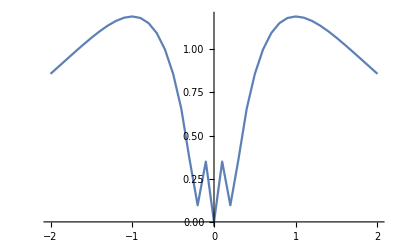

```mathematica
TablePlot[Abs[ρ[x]],{x,-2,2,0.1}]
```

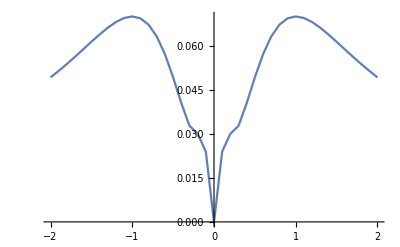

```mathematica
TablePlot[Abs[r[x]-ρ[x]],{x,-2,2,0.1}]
```

## Plotting: timestring outputs relevant computation times and region information

```mathematica
qSGgeneral=NotebookDirectory[]<>"qSG";
```

```mathematica
Get["qSG"];
```

```mathematica
qSG//Clear;
qSG[x_,t_]:=qSG[x,t]=SGAuto[x,t];
```

```mathematica
myacos[x_]:=Piecewise[{{ArcCos[Re[x[[1,1]]]],ArcSin[Re[x[[1,2]]]]>0},{2Pi-ArcCos[Re[x[[1,1]]]],ArcSin[Re[x[[2,1]]]]≤0}}];
```

```mathematica
xx=0;
tt=0;
qSG[xx,tt]
timestring
```

{{1.00001-1.61534×10^-13 ⅈ,0.0000385096-7.63905×10^-14 ⅈ},{-0.0000385092-1.62989×10^-13 ⅈ,1.00001-5.69872×10^-14 ⅈ}}

Region: 0 (0,0) 1) Construct: 82.8438  1) Solve: 1.60938  2) Construct: 3.26563  2) Solve: 0.890625

```mathematica
Det[qSG[xx,tt]]
```

1.00001-2.1852×10^-13 ⅈ

```mathematica
ans=qSG[xx,tt].{{1,0},{0,-1}}.Inverse[qSG[xx,tt]]
```

{{1.-6.67033×10^-18 ⅈ,-0.0000770187+1.52775×10^-13 ⅈ},{-0.0000770179-3.25987×10^-13 ⅈ,-1.+6.67033×10^-18 ⅈ}}

```mathematica
Cos[q[xx]]-ans[[1,1]]
Sin[q[xx]]-ans[[1,2]]
Sin[q[xx]]-ans[[2,1]]
```

2.96591×10^-9+6.67033×10^-18 ⅈ

0.0000770187-1.52775×10^-13 ⅈ

0.0000770179+3.25987×10^-13 ⅈ

```mathematica
myacos[ans]
q[xx]
```

6.28311

0

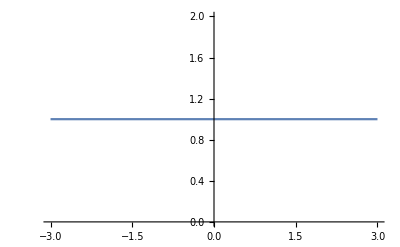

```mathematica
TablePlot[Cos[q[x]],{x,-3,3,0.1},PlotRange->All]
```

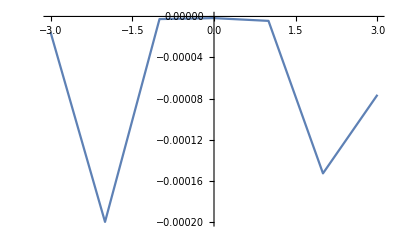

```mathematica
Monitor[TablePlot[Re[1+2*qSG[x,0][[1,2]]*qSG[x,0][[2,1]]]-Cos[q[x]],{x,-3,3,1},PlotRange->All],timestring]
```

```mathematica
TablePlot[Re[1+2*qSG[x,0][[1,2]]*qSG[x,0][[2,1]]]-Cos[q[x]],{x,-3,3,1},PlotRange->All]
```

#### Compare with linearized pde

```mathematica
xmin=-3;
xmax=3;
dx=0.2;
tmin=0;
tmax=30;
dt=0.5;
lmax=40;
```

```mathematica
(*solve linear eq*)Manipulate[
dd=0.2;
xx=Range[-LL,LL-dd,dd];
nq0=Table[q[x],{x,-LL,LL-dd,dd}];(*even number of points*)
nqt0=Table[qt[x],{x,-LL,LL-dd,dd}];(*even number of points*)
w=Pi/LL*Join[Range[0,Length[nq0]/2], Range[-Length[nq0]/2+1,-1]];
nhq0=Fourier[nq0];
nhqt0=Fourier[nqt0];
(*nhqt=Quiet[nhq0*Exp[I/w*tt]*I*w/.Indeterminate->0.];*)
nhqt=(nhq0*Cos[Sqrt[1+w^2]*tt]+nhqt0/Sqrt[1+w^2]*Sin[Sqrt[1+w^2]*tt])/.Indeterminate->0.;
nqt=InverseFourier[nhqt];
ListLinePlot[Cases[Table[{xx[[k]],Cos[Re[nqt[[k]]]]},{k,1,Length[nq0]}],{x_,y_}/;-LL≤x≤LL],PlotRange->All],{tt,0,10,0.1}]
```

```mathematica
FDsolver[NN_]:=Module[{},
ddt=1/NN/2;
ddx=1/NN;
xxx=Range[-lmax,lmax-ddx,ddx];
ttt=Range[tmin,tmax,ddt];
nq0=Table[q[x],{x,-lmax,lmax-ddx,ddx}];(*even number of points*)
nqt0=Table[qt[x],{x,-lmax,lmax-ddx,ddx}];(*even number of points*)
nx=Round[2*lmax/ddx]; 
nt=Round[tmax/ddt]+1;
qfd=ConstantArray[0,{nx,nt}];
For[j=1,j≤nx,j=j+1,
qfd[[j,1]]=nq0[[j]];
qfd[[j,2]]=nq0[[j]]+nqt0[[j]]*ddt;
];
For[n=1,n≤ nt-2,n++,
For[j=2,j≤nx-1,j=j+1,
qfd[[j,n+2]]=(ddt/ddx)^2*(qfd[[j+1,n+1]]-2qfd[[j,n+1]]+qfd[[j-1,n+1]])-ddt^2*Sin[qfd[[j,n+1]]]+2qfd[[j,n+1]]-qfd[[j,n]]
]
];
iqfd=Interpolation[Flatten[Table[{{xxx[[j]],ttt[[n]]},qfd[[j,n]]},{j,1,nx},{n,1,nt}],1]];
{qfd,iqfd}
]
```

```mathematica
Timing[qfd=FDsolver[2][[1]]][[1]]
```

$Aborted

```mathematica
FDsolver[2]
```

$Aborted

```mathematica
(*plot fd sol*)
Manipulate[
{ListLinePlot[Cases[Table[{xxx[[k]],Re[Cos[qfd[[k,tt]]]]},{k,1,nx,Round[nx/200]+1}],{x_,y_}/;-lmax≤x≤lmax],PlotRange->{-1,1}],ListLinePlot[Cases[Table[{xxx[[k]],Re[qfd[[k,tt]]]},{k,1,nx,Round[nx/200]+1}],{x_,y_}/;-lmax≤x≤lmax],PlotRange->All]},{tt,1,nt,Round[nt/30]+1}]
```

Table::iterb: Iterator {k,1,Round[20 lmax]} does not have appropriate bounds.

Part::pkspec1: The expression k cannot be used as a part specification.

```mathematica
(*plot interpolated fd sol*)
Manipulate[TablePlot[Cos[iqfd[x,tt]],{x,xmin,xmax,dx},PlotRange->{-1,1},InterpolationOrder->1,PlotStyle->Thick],{tt,tmin,tmax,dt}]
```

```mathematica
(*compute ist sol*)
Monitor[Table[qSG[x,tt],{x,xmin,xmax,dx},{tt,tmin,tmax,dt}],timestring];
Save[qSGgeneral,qSG];
```

```mathematica
Table[qSG[x,tt],{x,xmin,xmax,dx},{tt,tmin,tmax,dt}];
```

```mathematica
(*plot ist sol*)
Manipulate[
TablePlot[Re[1+2*qSG[x,tt][[1,2]]*qSG[x,tt][[2,1]]],{x,xmin,xmax,dx},PlotRange->{-1,1},InterpolationOrder->1,PlotStyle->Thick],{tt,tmin,tmax,dt}]
```

```mathematica
(*difference between fd and ist*)
Manipulate[
TablePlot[Re[1+2*qSG[x,tt][[1,2]]*qSG[x,tt][[2,1]]]-Cos[iqfd[x,tt]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],{tt,tmin,tmax,dt}]
```

```mathematica
Grhp2[[4]]//DCTPlot
```

### Debug Related

```mathematica
ListPlot3D[Flatten[Table[{x,y,Abs[G[0,0][x+I y][[1,2]]]},{x,-1/2,1/2,0.1},{y,-1/2,1/2,0.1}],1],AxesLabel->{x,y,z},PlotRange->All]
```

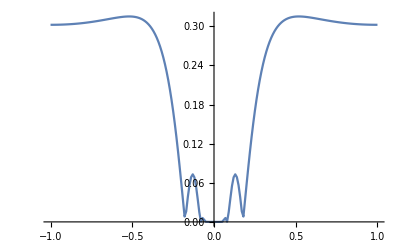

```mathematica
TablePlot[Abs[G[0,0][z][[2,1]]],{z,-1,1,0.01},PlotRange->All]
```

```mathematica
{out,phi,rhp1,rhp2,tt}=SG[0][0,0];
```

Private`PoleList[0,0]

```mathematica
out
```

{{1.-2.61924×10^-17 ⅈ,-9.07193×10^-7+1.61446×10^-14 ⅈ},{1.05074×10^-6+1.38608×10^-14 ⅈ,1.-3.20662×10^-17 ⅈ}}

```mathematica
phi[0]
```

{{1.-2.61924×10^-17 ⅈ,-9.07193×10^-7+1.61446×10^-14 ⅈ},{1.05074×10^-6+1.38608×10^-14 ⅈ,1.-3.20662×10^-17 ⅈ}}

```mathematica
rhp2
```

Private`rhp2$8428

```mathematica
RHSolved//Clear;
RHSolved[X_]:=RHSolved[X]=RHSolve[X];
RHSolved[{}]:=0.;
RHSolution[X_][z_]:=Cauchy[X//RHSolved,z]+IdentityMatrix[2];
```

```mathematica
RHSolution[rhp1][0]
```

{{0.540253-2.41751×10^-14 ⅈ,-0.84145+1.80897×10^-14 ⅈ},{0.841514+1.52933×10^-14 ⅈ,0.540317+2.72282×10^-14 ⅈ}}

```mathematica
RHSolution[rhp2][0]
```

{{1+Cauchy[0.,0],Cauchy[0.,0]},{Cauchy[0.,0],1+Cauchy[0.,0]}}

```mathematica
r[k_]:=ρ[k];
θ[x_,t_][z_]:=2 I (-t/4/z+x z);
rb[k_]:= cc[r[cc[k]]];
rbsamp[k_]:= cc[rsamp[cc[k]]];
τsamp[k_]:=1+ rsamp[k]cc[rsamp[cc[k]]];

G[x_,t_][z_]:=({{1+r[z]rb[z], rb[z]Exp[-θ[x,t][k]]}, {r[z] Exp[θ[x,t][k]], 1}});
G[_,_][_?InfinityQ]:=({{1., 0}, {0, 1.}});
```

```mathematica
J[0][0,0]
```

{{G[0,0][#1]&,G[0,0][#1]&},{Line[{-100,0}],Line[{0,100}]},{40,40}}

```mathematica
J[1][-10,0]
```

{{U[-10,0][#1]&,U[-10,0][#1]&,Private`DD[#1]&,L[-10,0][#1]&,L[-10,0][#1]&,Private`P[-10,0][#1]&,Private`P[-10,0][#1]&,Private`M[-10,0][#1]&,Private`M[-10,0][#1]&},{Line[{0.+0.4 ⅈ,99.6+0.4 ⅈ}],Line[{99.6+0.4 ⅈ,100}],Line[{0,100}],Line[{0.-0.4 ⅈ,99.6-0.4 ⅈ}],Line[{99.6-0.4 ⅈ,100}],Line[{100,100.4+0.4 ⅈ}],Line[{100.4+0.4 ⅈ,200.+0.4 ⅈ}],Line[{100,100.4-0.4 ⅈ}],Line[{100.4-0.4 ⅈ,200.-0.4 ⅈ}]},{20,20,20,20,20,20,20,20,20}}

```mathematica
Jadapt[1][-10,0]
```

{{U[-10,0][#1]&,Private`DD[#1]&,L[-10,0][#1]&},{Line[{0.+0.4 ⅈ,7.9125+0.4 ⅈ}],Line[{0,5.8625}],Line[{0.-0.4 ⅈ,7.9125-0.4 ⅈ}]},{40,40,40}}

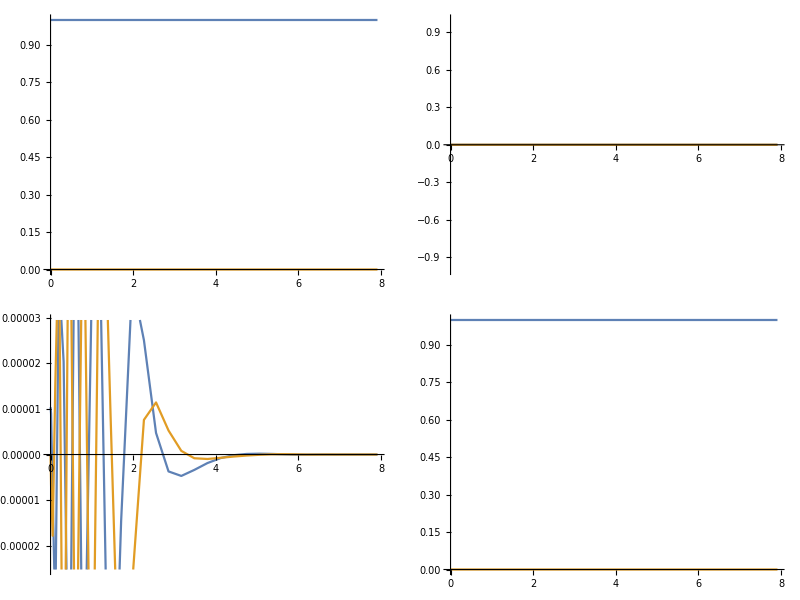
(-Graphics-)

```mathematica
ff=Fun[L[-10,0][#1]&,Line[{0.-0.4 ⅈ,7.912499999999998-0.4 ⅈ}],40]
```

```mathematica
L[-10,0][0]
```

{{1,0},{0.499885,1}}

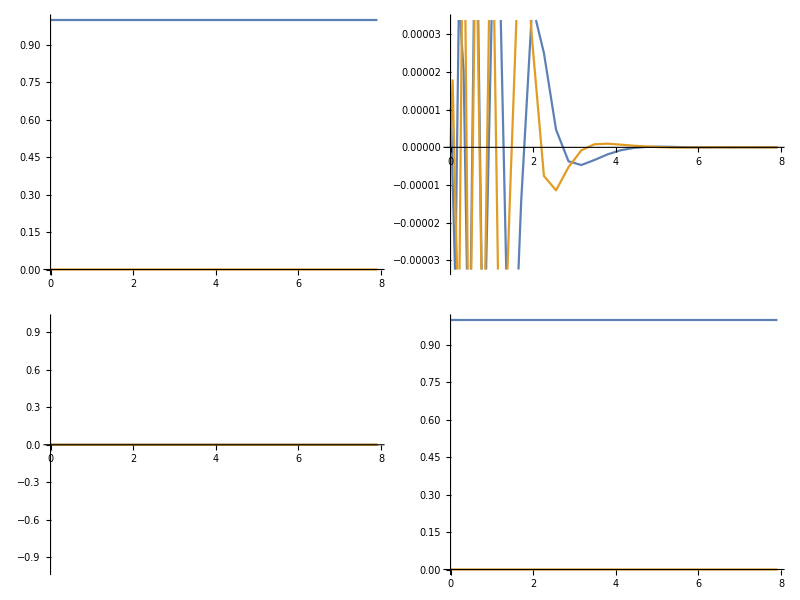
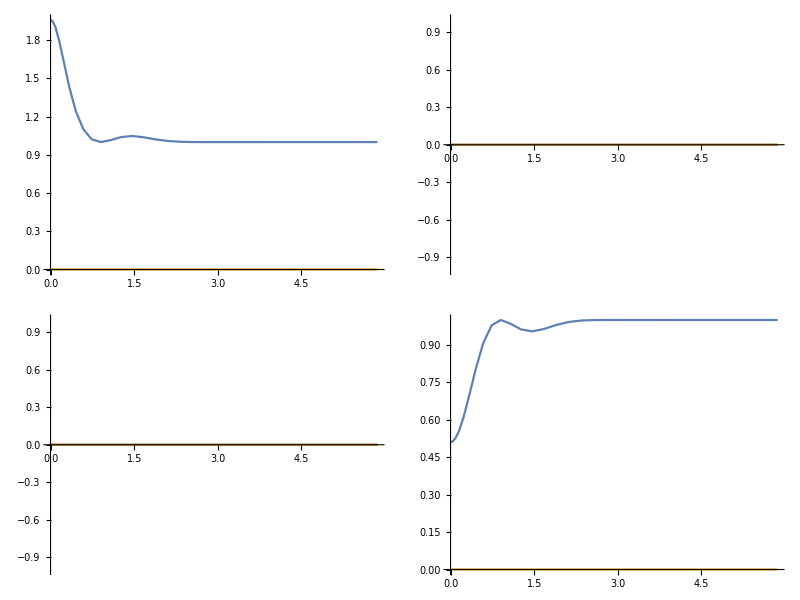
{(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
GG=Jadapt[1][-10,0]//MakeListFun
```

```mathematica
Grhp1[[1]][-1]
```

{{1.+2.71019×10^-8 ⅈ,-13985.2-18010.7 ⅈ},{0.+0. ⅈ,1.+1.49136×10^-8 ⅈ}}

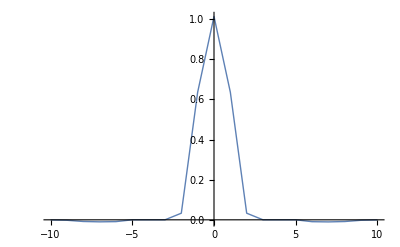

```mathematica
(* Focusing *)
Monitor[TablePlot[qNLS[x,0.0]//Re,{x,-10,10,1.},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

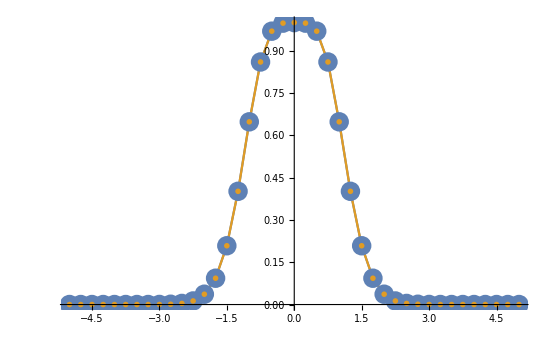

```mathematica
TablePlot[{qNLS[x,0.]//Re,Sech[x^2]},{x,-10,10,1.},PlotMarkers->{{●,20},{"x",30}}]
```

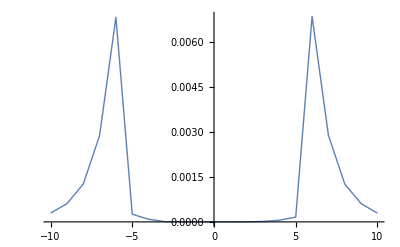

```mathematica
TablePlot[Abs[qNLS[x,0.]-Sech[x^2]],{x,-10,10,1.},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick]
```

```mathematica
TablePlot[Abs[qNLS[x,0.0]-Sech[x^2]]/Sech[x^2],{x,-10,10,1.},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick]
```

```mathematica
(* Defocusing *)
Monitor[TablePlot[qmKdV[x,1.]//Re,{x,-20,10,.25},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

$Aborted

RuleDelayed::rhs: Pattern mu_ appears on the right-hand side of rule pp[mu_,nn_]:>(pp[mu_,nn_]=LocatePolesSG[q,qx,qt,mu,nn]).

RuleDelayed::rhs: Pattern nn_ appears on the right-hand side of rule pp[mu_,nn_]:>(pp[mu_,nn_]=LocatePolesSG[q,qx,qt,mu,nn]).

$Aborted

LinearSolve::matrix: Argument {{«1»}+{(0.+0.000510204 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.-0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.+0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.-0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),«44»,(0.+0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.-0.000510204 ⅈ) (-1/Part[«2»]+{}⟦2⟧),«50»},«49»,«50»} at position 1 is not a non-empty rectangular matrix.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 50 of LinearSolve[{{1-{«50»}.DiagonalMatrix[«1»],«49»,«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},{«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},«47»,{«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«17»,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},«50»},«1»] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LinearSolve::matrix: Argument {{«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},«49»,«50»} at position 1 is not a non-empty rectangular matrix.

General::stop: Further output of LinearSolve::matrix will be suppressed during this calculation.

Inverse::matsq: Argument {{{«1»},{{1-Dot[«2»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],«38»,-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],«1»}+{«1»},«49»,«50»}},{«1»⟦51⟧,«1»}} at position 1 is not a non-empty square matrix.

$Aborted[]